```mathematica
QLFile = "/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/src/results/qlearn_L.dat";
QOFile = "/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/src/results/qlearn_O.dat";
QRFile = "/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/src/results/qlearn_R.dat";
```

```mathematica
VLFile="/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/src/results/track_convergence/L_track.txt";
VOFile="/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/src/results/track_convergence/O_track.txt";
VRFile="/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/src/results/track_convergence/R_track.txt";
```

```mathematica
QLData=ReadList[QLFile, Number];
QOData=ReadList[QOFile, Number];
QRData=ReadList[QRFile, Number];
```

```mathematica
VLData=ReadList[VLFile, Number];
VOData=ReadList[VOFile, Number];
VRData=ReadList[VRFile, Number];
```

```mathematica
dx = 20000;
```

```mathematica
BinQLData = Partition[QLData,dx];
BinQOData = Partition[QOData,dx];
BinQRData = Partition[QRData,dx];
```

```mathematica
AveQLData = Mean[BinQLData];
AveQOData = Mean[BinQOData];
AveQRData = Mean[BinQRData];
```

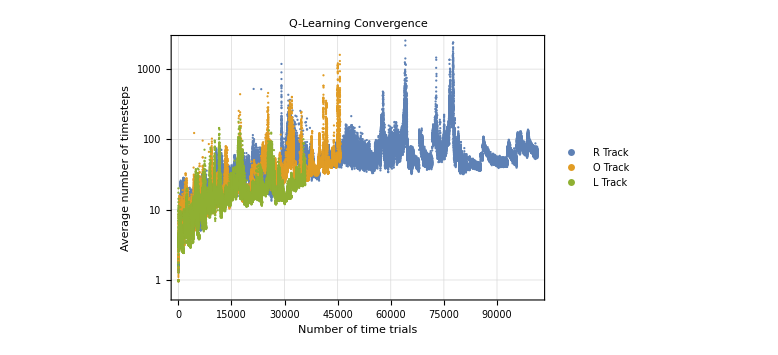

```mathematica
QPlot=ListLogPlot[{QRData,QOData,QLData}, PlotRange->All,ImageSize->Large,GridLines->Automatic,PlotLegends->{"R Track","O Track","L Track"},Frame-> True,FrameLabel->{"Number of time trials","Average number of timesteps"},PlotLabel->"Q-Learning Convergence"]
```

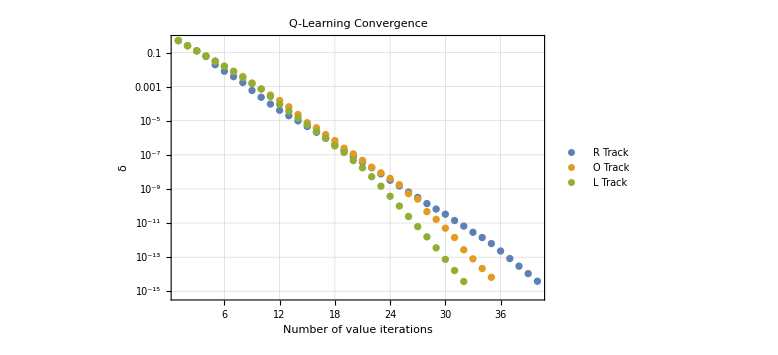

```mathematica
VPlot=ListLogPlot[{VRData,VOData,VLData}, PlotRange->All,ImageSize->Large,GridLines->Automatic,PlotLegends->{"R Track","O Track","L Track"},Frame-> True,FrameLabel->{"Number of value iterations",δ},PlotLabel->"Q-Learning Convergence"]
```

```mathematica
Export["/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/final_report/Diagrams/QLearn.eps",QPlot];
Export["/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project4_ReinforcementLearning/final_report/Diagrams/VIter.eps",VPlot];
```